# Problem Set 2.1

## Ex 1

```mathematica
Graphics3D[{{HalfPlane[{2,3,4},{1,0,0},{0,1,0}]},{HalfPlane[{2,3,4},{1,0,0},{0,0,1}]},{HalfPlane[{2,3,4},{0,1,0},{0,0,1}]}, {Arrow[{{0,0,0},{2,0,0}}]},{Arrow[{{0,0,0},{0,3,0}}]},{Arrow[{{0,0,0},{0,0,4}}]},{Pink,Arrow[{{0,0,0},{2,3,4}}]}},Axes->True,AxesLabel->{x,y,z}]
ClearAll
```

-Graphics3D-

ClearAll

## Ex 1I

Yes, they are the same.

```mathematica
Graphics3D[{{HalfPlane[{2,0,0},{0,3,0},{0,0,4}]},{HalfPlane[{0,3,0},{2,0,0},{0,0,4}]},{HalfPlane[{0,0,4},{0,3,0},{2,0,0}]},{Arrow[{{0,0,0},{2,0,0}}]},{Arrow[{{0,0,0},{0,3,0}}]},{Arrow[{{0,0,0},{0,0,4}}]},{Pink,Arrow[{{0,0,0},{2,3,4}}]}},Axes->True,AxesLabel->{x,y,z}]
ClearAll
```

-Graphics3D-

ClearAll

## Ex III

2x+0y+0z=4
2x+3y+0z=13
0x+0y+4z=16
CHANGED: row picture, column picture,coefficient matrix.
The solution is still the same.

```mathematica
Graphics3D[{{HalfPlane[{2,0,0},{0,0,1},{0,1,0}]},{HalfPlane[{{2,3,0},{0,13/3,0}},{0,0,1}]},{Red,HalfPlane[{0,0,4},{1,0,0},{0,1,0}]},{Arrow[{{0,0,0},{2,2,0}}]},{Arrow[{{0,0,0},{0,3,0}}]},{Arrow[{{0,0,0},{0,0,4}}]},{Pink,Arrow[{{0,0,0},{4,9,16}}]}},Axes->True, AxesLabel->{x,y,z}]
ClearAll
```

-Graphics3D-

ClearAll

## Ex IV

reta: 2x+4z=10, if z=2 then x=1 for all y
if z=0 then x=5. In between this points there is z=1 with x=

```mathematica
ClearAll
Plot3D[{(x+y-6)/(-3),4-x+y,10/4-x/2},{x,-10,10},{y,-2,2},AxesLabel->{x,y,z}]
```

ClearAll

-Graphics3D-

## Ex V

```mathematica
Plot3D[{2-x-y,3-x-2y,(5-2x-3y)/2},{x,-2,2},{y,-2,2},AxesLabel->{x,y,z}]
```

-Graphics3D-

The third plane contains that line, because
if x, y, z satisfy the first two equations then they also satisfy the third equation.

## Ex VI

```mathematica
Plot3D[{2-x-y,3-x-2y,(9-2x-3y)/2},{x,-2,2},{y,-1,3},AxesLabel->{x,y,z}]
ClearAll
```

-Graphics3D-

ClearAll

Now the three equations have no solution because they don’t meet at a single point. The first two planes meet along the line L, but the third plane doesn’t cross that line.

## Ex VII

This is a “singular case” because the third column is igual the fisrt column. c=10

```mathematica
LinearSolve[Transpose[{{1,1,2},{1,2,3},{1,1,2}}],{2,3,5}]
LinearSolve[Transpose[{{1,1},{1,2}}],{4,6}]
c={2,3}.LinearSolve[Transpose[{{1,1},{1,2}}],{4,6}]
```

{1,1,0}

{2,2}

10

## Ex VIII

Normally 4 “planes” in 4-dimensional space meet at a point. Normally 4 column
vectors in 4-dimensional space can combine to produce b. We are solving
x+y+z+t=3
y+z+t=3
z+t=3
t=2

```mathematica
LinearSolve[Transpose[{{1,0,0,0},{1,1,0,0},{1,1,1,0},{1,1,1,1}}],{3,3,3,2}]
ClearAll
```

{0,0,1,2}

ClearAll

## Ex IX & X

```mathematica
LinearSolve[2*{1,-2,-4}+2*{2,3,1}+3*{4,1,2}]
LinearSolve[{{1,2,4},{-2,3,1},{-4,1,2}}.{2,2,3}]
```

LinearSolve::matrix: Argument {18,5,0} at position 1 is not a non-empty rectangular matrix.

LinearSolve[{18,5,0}]

LinearSolve::matrix: Argument {18,5,0} at position 1 is not a non-empty rectangular matrix.

LinearSolve[{18,5,0}]

```mathematica
LinearSolve[{2,1,0,0}+{1,2,1,0}+{0,1,2,1}+2*{0,0,1,2}]
LinearSolve[{{2,1,0,0},{1,2,1,0},{0,1,2,1},{0,0,1,2}}.{1,1,1,2}]
ClearAll
```

LinearSolve::matrix: Argument {3,4,5,5} at position 1 is not a non-empty rectangular matrix.

LinearSolve[{3,4,5,5}]

LinearSolve::matrix: Argument {3,4,5,5} at position 1 is not a non-empty rectangular matrix.

LinearSolve[{3,4,5,5}]

ClearAll

It’s necesary to do 9 separate multiplications.

## Ex XI

```mathematica
LinearSolve[{{2,3},{5,1}}.{4,2}]
```

LinearSolve::matrix: Argument {14,22} at position 1 is not a non-empty rectangular matrix.

LinearSolve[{14,22}]

```mathematica
LinearSolve[2*{3,6}+(-1)*{6,12}]
```

LinearSolve::matrix: Argument {0,0} at position 1 is not a non-empty rectangular matrix.

LinearSolve[{0,0}]

```mathematica
LinearSolve[{{1,2,4},{2,0,1}}.{3,1,1}]
LinearSolve[3*{1,2}+{2,0}+{4,1}]
```

LinearSolve::matrix: Argument {9,7} at position 1 is not a non-empty rectangular matrix.

LinearSolve[{9,7}]

LinearSolve::matrix: Argument {9,7} at position 1 is not a non-empty rectangular matrix.

LinearSolve[{9,7}]

## Ex XII

```mathematica
LinearSolve[{{0,0,1},{0,1,0},{1,0,0}}.{x,y,z}]
```

LinearSolve::matrix: Argument {z,y,x} at position 1 is not a non-empty rectangular matrix.

LinearSolve[{z,y,x}]

```mathematica
LinearSolve[{2,1,3}+{1,2,3}-{3,3,6}]
```

LinearSolve::matrix: Argument {0,0,0} at position 1 is not a non-empty rectangular matrix.

LinearSolve[{0,0,0}]

```mathematica
LinearSolve[{{2,1},{1,2},{3,3}}.{1,1}]
LinearSolve[{2,1,3}+{1,2,3}]
ClearAll
```

LinearSolve::matrix: Argument {3,3,6} at position 1 is not a non-empty rectangular matrix.

LinearSolve[{3,3,6}]

LinearSolve::matrix: Argument {3,3,6} at position 1 is not a non-empty rectangular matrix.

LinearSolve[{3,3,6}]

ClearAll

## Ex XIII

(a) A matrix with m rows and n columns multiplies a vector with  n components
to produce a vector with m components.
(b) The planes from the m equations Ax = b are in n-dimensional space.
The combination of the columns of A is in m-dimensional space.

## Ex XIV

How do I hoose the 8 position????

```mathematica
({{2, 0, 0, 0}, {0, 3, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 5}}).Transpose[{x,y,z,t}]=Transpose[{8,0,0,0}]
```

```mathematica
LinearSolve[{{2,0,0,0},{0,3,0,0},{0,0,1,0},{0,0,0,5}},{8,0,0,0}]
Manipulate[Plot3D[{-2*x-3*y-5*t+8},{x,-1,1},{y,-1,1}],{t,-10,10}]
ClearAll
```

{4,0,0,0}

ClearAll

## Ex XV

```mathematica
a -    ({{1, 0}, {0, 1}}).Transpose[{x,y}]=Transpose[{x,y}]
b -    ({{0, 1}, {1, 0}}).Transpose[{x,y}]=Transpose[{y,x}]
```

## Ex XVI

```mathematica
a -    ({{0, 1}, {-1, 0}}).Transpose[{x,y}]=Transpose[{x,y}]
b -    ({{-1, 0}, {0, -1}}).Transpose[{x,y}]=Transpose[{-x,-y}]
```

## Ex XVII

```mathematica
({{0, 1, 0}, {0, 0, 1}, {1, 0, 0}}).Transpose[{x,y,z}]=Transpose[{y,z,x}]
({{0, 0, 1}, {1, 0, 0}, {0, 1, 0}}).Transpose[{y,z,x}]=Transpose[{x,y,z}]
```

## Ex XVIII

```mathematica
({{1, 0}, {-1, 1}}).Transpose[{x,y}]=Transpose[{x,y-x}]
```

```mathematica
({{1, 0, 0}, {-1, 1, 0}, {0, 0, 1}}).Transpose[{x,y,z}]=Transpose[{x,y-x,z}]
```

```mathematica
LinearSolve[{{1,0},{-1,1}}.{3,5}]
LinearSolve[{{1,0,0},{-1,1,0},{0,0,1}}.{3,5,7}]
ClearAll
```

LinearSolve::matrix: Argument {3,2} at position 1 is not a non-empty rectangular matrix.

LinearSolve[{3,2}]

LinearSolve::matrix: Argument {3,2,7} at position 1 is not a non-empty rectangular matrix.

LinearSolve[{3,2,7}]

ClearAll

## Ex XIX

```mathematica
({{1, 0, 0}, {0, 1, 0}, {1, 0, 1}}).Transpose[{x,y,z}]=Transpose[{x,y,z+x}]
```

```mathematica
({{1, 0, 0}, {0, 1, 0}, {-1, 0, 1}}).Transpose[{x,y,z}]=Transpose[{x,y,z+x}]
```

```mathematica
LinearSolve[{{1,0,0},{0,1,0},{1,0,1}}.{3,4,5}]
LinearSolve[{{1,0,0},{0,1,0},{-1,0,1}}.{3,4,8}]
ClearAll
```

LinearSolve::matrix: Argument {3,4,8} at position 1 is not a non-empty rectangular matrix.

LinearSolve[{3,4,8}]

LinearSolve::matrix: Argument {3,4,5} at position 1 is not a non-empty rectangular matrix.

LinearSolve[{3,4,5}]

ClearAll

If you multiply (3,4,5) by E and then
multiply by E^-1 , the two results are (3,4,8) and ( 3,4,5).

## Ex XX

```mathematica
({{1, 0}, {0, 0}}).Transpose[{x,y}]=Transpose[{x,0}]
({{0, 0}, {0, 1}}).Transpose[{x,y}]=Transpose[{0,y}]
```

```mathematica
LinearSolve[{{1,0},{0,0}}.{5,7}]
LinearSolve[{{0,0},{0,1}}.{{1,0},{0,0}}.{5,7}]
ClearAll
```

LinearSolve::matrix: Argument {5,0} at position 1 is not a non-empty rectangular matrix.

LinearSolve[{5,0}]

LinearSolve::matrix: Argument {0,0} at position 1 is not a non-empty rectangular matrix.

LinearSolve[{0,0}]

ClearAll

## Ex XXI

```mathematica
({{(√2)/2, -(√2)/2}, {(√2)/2, (√2)/2}}).Transpose[{x,y}]=Transpose[{1/2 √2 (x-y),1/2 √2 (x+y)}]
({{(√2)/2, -(√2)/2}, {(√2)/2, (√2)/2}}).Transpose[{1,0}]=Transpose[{(√2)/2,(√2)/2}]
({{(√2)/2, -(√2)/2}, {(√2)/2, (√2)/2}}).Transpose[{0,1}]=Transpose[{(-√2)/2,(√2)/2}]
```

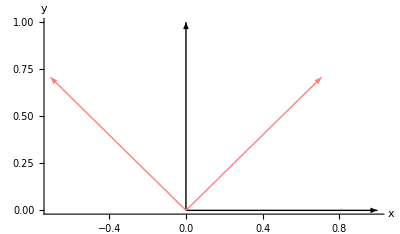

```mathematica
Graphics[{{Arrow[{{0, 0}, {1, 0}}]}, {Arrow[{{0, 0}, {0, 1}}]}, 
  {Pink,Arrow[{{0, 0}, {Sqrt[2]/2, Sqrt[2]/2}}]}, 
  {Pink,Arrow[{{0, 0}, {-(Sqrt[2]/2), Sqrt[2]/2}}]}},Axes->True,AxesLabel->{x,y}]
```

## Ex XXII

```mathematica
({{1, 4, 5}}).Transpose[({{x, y, z}})]=0
```

```mathematica
LinearSolve[{1,4,5},0]
```

LinearSolve::matrix: Argument {1,4,5} at position 1 is not a non-empty rectangular matrix.

```mathematica
LinearSolve[{1,4,5},{0}]
```

LinearSolve::matrix: Argument {1,4,5} at position 1 is not a non-empty rectangular matrix.

```mathematica
Solve[{1,4,5}.{x,y,z}==0]
ClearAll
```

Dot::rect: Nonrectangular tensor encountered.

{{{1,4,5}.{{5,-2},y,z}→0}}

ClearAll

The solutions to Ax = 0 lie on a plane perpendicular to the vector. The columns of A are only in 1-dimensional space.

## Ex XXIII

```mathematica
A={{1,2},{3,4}}
x={5,-2}
b={1,7}
LinearSolve[A.x]
ClearAll
```

{{1,2},{3,4}}

{5,-2}

{1,7}

LinearSolve::matrix: Argument {1,7} at position 1 is not a non-empty rectangular matrix.

LinearSolve[{1,7}]

ClearAll

## Ex XXIV

```mathematica
A= {{1,0,0},{0,1,0},{0,0,1}}
v={3,4,5}
LinearSolve[A.v]
```

{{1,0,0},{0,1,0},{0,0,1}}

{3,4,5}

LinearSolve::matrix: Argument {3,4,5} at position 1 is not a non-empty rectangular matrix.

LinearSolve[{3,4,5}]

```mathematica
LinearSolve[Transpose[v].v]
```

Transpose::nmtx: The first two levels of {3,4,5} cannot be transposed.

```mathematica
Solve[{3,4,5}.({{3}, {4}, {5}})]
```

Solve::naqs: 50 is not a quantified system of equations and inequalities.

```mathematica
Solve[{50}]
ClearAll
```

Solve::naqs: 50 is not a quantified system of equations and inequalities.

Solve[{50}]

ClearAll

## Ex XXV

```mathematica
Solve[{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}.{1,0,0,0}]
```

Solve::naqs: 1&&0&&0&&0 is not a quantified system of equations and inequalities.

Solve[{1,0,0,0}]

```mathematica
Solve[{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}.{1,0,0,0}]
ClearAll
```

Solve::naqs: 1&&0&&0&&0 is not a quantified system of equations and inequalities.

Solve[{1,0,0,0}]

ClearAll

What does eye(4) do?

## Ex XXVI

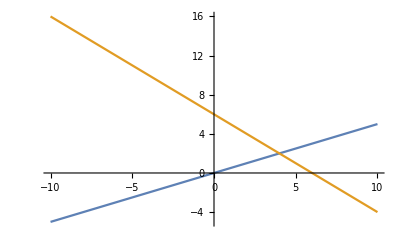

```mathematica
x=.
Plot[{x/2,6-x},{x,-10,10}]
```

```mathematica
Graphics3D[{{Arrow[{{0,0,0},4*{1,1,0}}]},{Arrow[{{0,0,0},2*{-2,1,0}}]},{Pink,Arrow[{{0,0,0},{0,6,0}}]}},Axes->True,AxesLabel->{x,y,z}]
```

-Graphics3D-

## Ex XXVII

For two linear equations in three unknowns x, y, Z, the row picture will show (2 or 3)
(lines or planes) in (2 or 3)-dimensional space. The column picture is in (2 or 3)dimensional
space. The solutions normally lie on a plane.

## Ex XXVIII

For four linear equations in two unknowns x and y, the row picture shows four
lines. The column picture is in 4-dimensional space. The equations have no
solution unless the vector on the right side is a linear combination of the vectors on the left side.

## Ex XXIX

```mathematica
u0={1,0}
A={{0.8,0.3},{0.2,0.7}}
u1=Solve[A.u0]
u2=Solve[A.{0.8,0.2}]
u3=Solve[A.{0.7,0.3}]
```

{1,0}

{{0.8,0.3},{0.2,0.7}}

Solve::naqs: 0.8&&0.2 is not a quantified system of equations and inequalities.

Solve[{0.8,0.2}]

Solve::naqs: 0.7&&0.3 is not a quantified system of equations and inequalities.

Solve[{0.7,0.3}]

Solve::naqs: 0.65&&0.35 is not a quantified system of equations and inequalities.

Solve[{0.65,0.35}]

Aplicaçoes sucessivas parecem fazer com que os vetores tendam a {0.6,0.4}  e la permaneçam, pela série 1/2^k.

## Ex XXX

```mathematica
u0={1,0}
A={{0.8,0.3},{0.2,0.7}}
u1=Solve[A.u0]
u2=Solve[A.{0.8,0.2}]
u3=Solve[A.{0.7,0.3}]
u4=Solve[A.{0.65,0.35}]
u5=Solve[A.{0.625,0.375}]
u6=Solve[A.{0.6125,0.3875}]
u7=Solve[A.{0.6062500000000001,0.39375}]
un=Solve[A.{0.6,0.4}]
v0={0,1}
v1=Solve[A.v0]
v2=Solve[A.{0.3,0.7}]
v3=Solve[A.{0.45,0.55}]
v4=Solve[A.{0.525,0.475}]
v5=Solve[A.{0.5625,0.4375}]
v6=Solve[A.{0.58125,0.41874999999999996}]
v7=Solve[A.{0.5906250000000001,0.409375}]
vn=Solve[A.{0.6,0.4}]
```

{1,0}

{{0.8,0.3},{0.2,0.7}}

Solve::naqs: 0.8&&0.2 is not a quantified system of equations and inequalities.

Solve[{0.8,0.2}]

Solve::naqs: 0.7&&0.3 is not a quantified system of equations and inequalities.

Solve[{0.7,0.3}]

Solve::naqs: 0.65&&0.35 is not a quantified system of equations and inequalities.

Solve[{0.65,0.35}]

Solve::naqs: 0.625&&0.375 is not a quantified system of equations and inequalities.

Solve[{0.625,0.375}]

Solve::naqs: 0.6125&&0.3875 is not a quantified system of equations and inequalities.

Solve[{0.6125,0.3875}]

Solve::naqs: 0.60625&&0.39375 is not a quantified system of equations and inequalities.

Solve[{0.60625,0.39375}]

Solve::naqs: 0.603125&&0.396875 is not a quantified system of equations and inequalities.

Solve[{0.603125,0.396875}]

Solve::naqs: 0.6&&0.4 is not a quantified system of equations and inequalities.

Solve[{0.6,0.4}]

{0,1}

Solve::naqs: 0.3&&0.7 is not a quantified system of equations and inequalities.

Solve[{0.3,0.7}]

Solve::naqs: 0.45&&0.55 is not a quantified system of equations and inequalities.

Solve[{0.45,0.55}]

Solve::naqs: 0.525&&0.475 is not a quantified system of equations and inequalities.

Solve[{0.525,0.475}]

Solve::naqs: 0.5625&&0.4375 is not a quantified system of equations and inequalities.

Solve[{0.5625,0.4375}]

Solve::naqs: 0.58125&&0.41875 is not a quantified system of equations and inequalities.

Solve[{0.58125,0.41875}]

Solve::naqs: 0.590625&&0.409375 is not a quantified system of equations and inequalities.

Solve[{0.590625,0.409375}]

Solve::naqs: 0.595313&&0.404688 is not a quantified system of equations and inequalities.

Solve[{0.595313,0.404688}]

Solve::naqs: 0.6&&0.4 is not a quantified system of equations and inequalities.

Solve[{0.6,0.4}]

## Ex XXXI

```mathematica
M3=({{8, 3, 4}, {1, 5, 9}, {6, 7, 2}})
Solve[M3.{1,1,1}]
M4=({{1, 15, 14, 4}, {12, 6, 7, 9}, {8, 10, 11, 5}, {13, 3, 2, 16}})
Solve[M4.{1,1,1,1}]
```

{{8,3,4},{1,5,9},{6,7,2}}

Solve::naqs: 15&&15&&15 is not a quantified system of equations and inequalities.

Solve[{15,15,15}]

{{1,15,14,4},{12,6,7,9},{8,10,11,5},{13,3,2,16}}

Solve::naqs: 34&&34&&34&&34 is not a quantified system of equations and inequalities.

Solve[{34,34,34,34}]

## Ex XXXII

if w = a*u+b*v, a e b constants, them the Matrix is singular.

```mathematica
Manipulate[Graphics3D[{{Arrow[{{0,0,0},b1*{1,0,0}}]},{Arrow[{{0,0,0},b2*{0,1,0}}]},{Arrow[{{0,0,0},{b1,b2,0}}]}}]
Plot3D[{x+2*b1,y+2*b2,(x+y+b1+b2)/2},{x,-10,10},{y,-10,10}],{b1,-10,10},{b2,-10,10}]
```

## Ex XXXIII

```mathematica
LinearSolve[{{1,0},{0,1}},{5,7}]
ClearAll
```

{5,7}

ClearAll

Aw=5*A*u+7*A*v

## Ex XXXIV

```mathematica
A=.
b=.
A=({{-1, 2, -1, 0, 0, 0}, {0, -1, 2, -1, 0, 0}, {0, 0, -1, 2, -1, 0}, {0, 0, 0, -1, 2, -1}})
b={1,2,3,4}
LinearSolve[A,b]
Solve[Inverse[A] . {-30, -20, -11, -4, 0, 0}]
```

{{-1,2,-1,0,0,0},{0,-1,2,-1,0,0},{0,0,-1,2,-1,0},{0,0,0,-1,2,-1}}

{1,2,3,4}

{-30,-20,-11,-4,0,0}

Inverse::matsq: Argument {{-1,2,-1,0,0,0},{0,-1,2,-1,0,0},{0,0,-1,2,-1,0},{0,0,0,-1,2,-1}} at position 1 is not a non-empty square matrix.

Solve::naqs: Inverse[{{-1,2,-1,0,0,0},{0,-1,2,-1,0,0},{0,0,-1,2,-1,0},{0,0,0,-1,2,-1}}].{-30,-20,-11,-4,0,0} is not a quantified system of equations and inequalities.

```mathematica
Solve[Inverse[{{-1,2,-1,0,0,0},{0,-1,2,-1,0,0},{0,0,-1,2,-1,0},{0,0,0,-1,2,-1}}].{-30,-20,-11,-4,0,0}]
```

## Ex XXXV

Sx is a 9x9 diagonal matrix whose non-zero elements are the number 1,2,...9, without repetition.

ClearAll

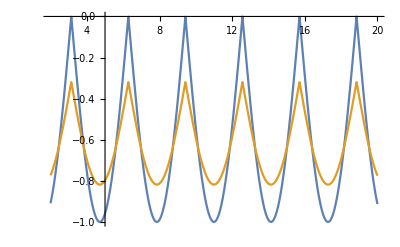

```mathematica
ClearAll
Plot[{-Abs[Sin[x]],-2/Pi+2*Sum[Cos[2*n*x]/(Pi(4*n^2-1)),{n,1,100}]},{x,2,20}]
```

ClearAll

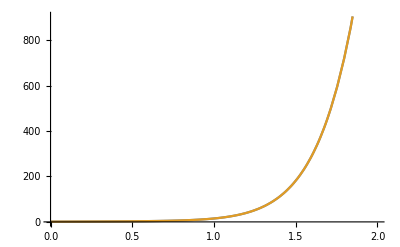

```mathematica
ClearAll
Plot[{1+2*x+x^2+2*x^3+x^4+2*x^5+x^6+2*x^7+x^8+2*x^9,Sum[1/2*(3+(-1)^(n+1))*x^n,{n,0,9}]},{x,0,2}]
```

```mathematica
Integral[]
```